```mathematica
pwsRAD21Data = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Paper Draft/Updated Draft/New/Science Version/Submission Materials/Source Code/Data for code/RAD21 depletion PWS data.xlsx","Data"][[1]];
```

```mathematica
pwsRAD21Data[[1]]
```

{HCT116 RAD21-AID2 (- Auxin),HCT116 RAD21-AID2 (+ 4 hr Auxin)}

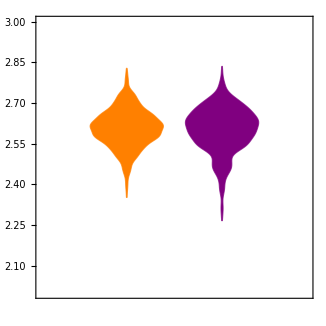

```mathematica
DistributionChart[
{
Select[Transpose[pwsRAD21Data][[1,2;;]],NumericQ[#]&],
Select[Transpose[pwsRAD21Data][[2,2;;]],NumericQ[#]&]
},
 AspectRatio->1, BarSpacing->Small, ChartStyle->{Orange, Purple}, ChartBaseStyle->EdgeForm[Thick], PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{All,{2,3}}]
```

```mathematica
TTest[{
Select[Transpose[pwsRAD21Data][[1,2;;]],NumericQ[#]&],Select[Transpose[pwsRAD21Data][[2,2;;]],NumericQ[#]&]}]
```

TTest::nortst: At least one of the p-values in {0.00954093,0}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

0.104216

```mathematica
Mean[Select[Transpose[pwsRAD21Data][[1,2;;]],NumericQ[#]&]]
Mean[Select[Transpose[pwsRAD21Data][[2,2;;]],NumericQ[#]&]]
```

2.60584

2.5998

```mathematica
StandardDeviation[Select[Transpose[pwsRAD21Data][[1,2;;]],NumericQ[#]&]]
StandardDeviation[Select[Transpose[pwsRAD21Data][[2,2;;]],NumericQ[#]&]]
```

0.0717815

0.0868889